```mathematica
vmax=11;
p=0.1;
rho=Round[(1-p)/(vmax+1-2*p),0.001];
dmin=Round[rho*0.1,0.001];
dmax=Round[rho*1.2,0.001];
dd=Round[(dmax-dmin)/22,0.001];
rho " :Transition density!!!"
dmin ": Min density"
dmax ": Max density"
dd ": density step"
"List of simulated values:"
For[i=-1,i<20,i++;
Print[dmin+i*dd]
]
For[i=1,i<4,i++;
Print[i*rho]
]
```

0.076  :Transition density!!!

0.008 : Min density

0.091 : Max density

0.004 : density step

List of simulated values:

0.008

0.012

0.016

0.02

0.024

0.028

0.032

0.036

0.04

0.044

0.048

0.052

0.056

0.06

0.064

0.068

0.072

0.076

0.08

0.084

0.088

0.152

0.228

0.304

```mathematica
RHT={{0.02,1.010062739409998}}
DHTOR={{0.02,0.010034130639991075}}
MFVOR={{0.02,0.0053437224928625186}}
FTDBZ={{0.02,3}}
```

{{0.02,1.01006}}

{{0.02,0.0100341}}

{{0.02,0.00534372}}

{{0.02,3}}

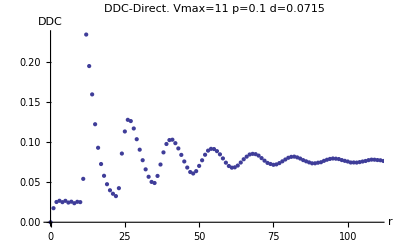

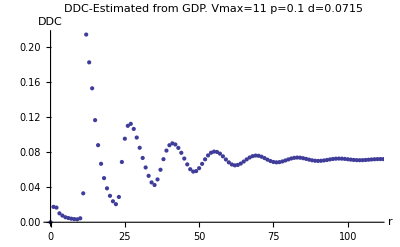

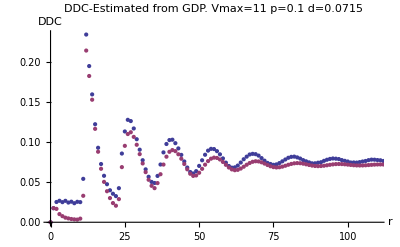

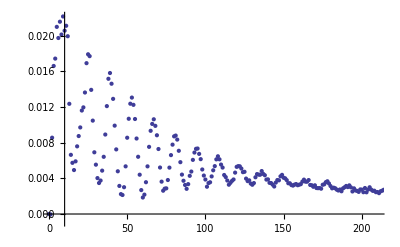

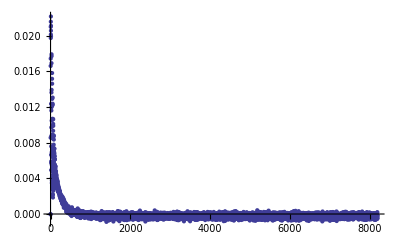

16384. = L

1171 = N

0.0714155 = (N-1)/(L-1)

585. = (N-1)/2

584.964  : Sum of DDC-Half Track

585.017  : Sum of OZ-Half Track

-0.0521937  : Sum of Δ

0.071563  : DDC-Averaged around L/2

0.0717971  : OZ-Averaged around L/2

1.00327  : Ratio at Half Track

0.00327807  : Δ at half track over random value

0.14806 = Mean of first 5*vmax values/Random Mean of DDC

502  : First time Δ becomes 0

```mathematica
d="0.0715";
p="0.1";
vmax="11";
n=16384.000;
j=StringToStream[d];
o= Read[j,Number];
m=Floor[o*16384];
prand=(m-1)/(n-1);
m2=(m-1)/2.;  
ddcc="/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax11/short/DDCCheck.d";
ddc="/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax11/short/ddensitycorrelation.d";
g=".p"<>p<>".v11.txt";
ddccadd=ddcc<>d<>g;
ddcadd=ddc<>d<>g;
DDCC=ReadList[ddccadd,{Number,Number}];
DDC=ReadList[ddcadd,{Number,Number}];
ListPlot[DDC,PlotLabel->"DDC-Direct.  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,"DDC"},PlotRange->{{0,110},Full}]
ListPlot[DDCC,PlotLabel->"DDC-Estimated from GDP.  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,"DDC"},PlotRange->{{0,110},Full}]
ListPlot[{DDC,DDCC},PlotLabel->"DDC-Estimated from GDP.  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,"DDC"},PlotRange->{{0,110},Full}]
DDC2=DDC[[All,2]];
DDCC2=DDCC[[All,2]];
dif=Table[{i-1,DDC2[[i]]-DDCC2[[i]]},{i,1,n/2+1}];
dif2=dif[[All,2]];
ListPlot[dif,PlotLabel->"Δ  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,"DDC"},PlotRange->{{1,210},Full}]
ListPlot[dif,PlotLabel->"Δ  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,"DDC"},PlotRange->Full]
n "= L"
m  "= N  "
prand  "= (N-1)/(L-1)"
m2 "= (N-1)/2"
Sum[DDC2[[i]],{i,1,n/2}] " : Sum of DDC-Half Track"
Sum[DDCC2[[i]],{i,1,n/2}]  " : Sum of OZ-Half Track"
Sum[dif2[[i]],{i,1,n/2}]  " : Sum of Δ"
DDCF=Sum[DDC2[[i]],{i,n/2-20*11,n/2}]/(20*11);
DDCF  " : DDC-Averaged around L/2"
DDCCF=Sum[DDCC2[[i]],{i,n/2-20*11,n/2}]/(20*11);
DDCCF " : OZ-Averaged around L/2"
DDCCF/DDCF " : Ratio at Half Track"
(DDCCF-DDCF)/prand  " : Δ at half track over random value"
diff=Table[{i,(DDC2[[i]]-DDCC2[[i]])},{i,0,16383}];
diff2=diff[[All,2]];
sum=Sum[Abs[diff2[[i]]],{i,1,55}]/(55);
sum/prand  "= Mean of first 5*vmax values/Random Mean of DDC"
x=3; While[dif2[[x]]>0.00005,x++]
x " : First time Δ becomes 0"
RHT=Append[RHT,{o,DDCCF/DDCF}];
DHTOR=Append[DHTOR,{o,(DDCCF-DDCF)/prand }];
MFVOR=Append[MFVOR,{o,sum/prand}];
FTDBZ=Append[FTDBZ,{o,x}];
```

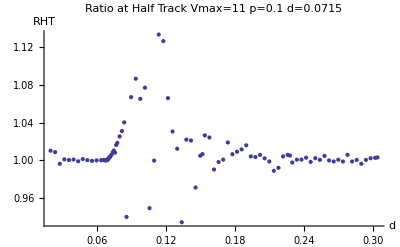

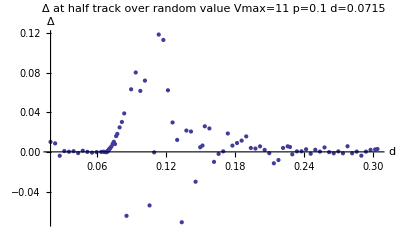

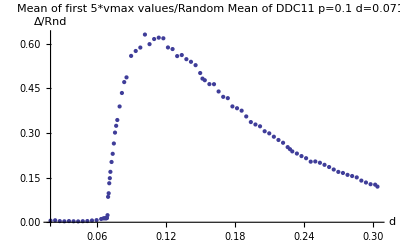

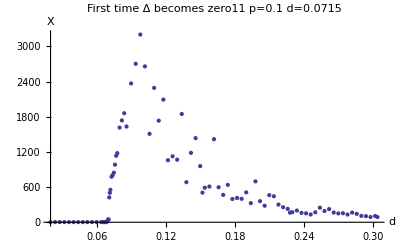

```mathematica
ListPlot[RHT,PlotLabel->"Ratio at Half Track  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{"d","RHT"},PlotRange->Full]
ListPlot[DHTOR,PlotLabel->"Δ at half track over random value  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{"d","Δ"},PlotRange->Full]
ListPlot[MFVOR ,PlotLabel->"Mean of first 5*vmax values/Random Mean of DDC"<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{"d","Δ/Rnd"},PlotRange->Full]
ListPlot[FTDBZ,PlotLabel->"First time Δ becomes zero"<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{"d","X"},PlotRange->Full]
```

```mathematica
RHT
DHTOR
MFVOR
FTDBZ
```

{{0.02,1.01006},{0.024,1.00857},{0.028,0.9961},{0.032,1.00083},{0.036,1.00014},{0.04,1.00069},{0.044,0.99881},{0.048,1.00118},{0.052,0.999992},{0.056,0.999258},{0.06,0.99973},{0.064,0.999955},{0.066,1.00018},{0.068,0.999615},{0.07,1.00145},{0.072,1.00411},{0.074,1.00823},{0.076,1.00797},{0.078,1.01837},{0.08,1.02519},{0.082,1.03095},{0.084,1.04015},{0.086,0.939669},{0.09,1.06702},{0.094,1.08659},{0.098,1.0652},{0.102,1.07704},{0.106,0.94898},{0.11,0.999504},{0.114,1.13352},{0.118,1.12657},{0.122,1.06592},{0.152,1.00641},{0.228,1.00494},{0.304,1.00288},{0.126,1.03041},{0.13,1.01215},{0.134,0.933994},{0.138,1.02188},{0.142,1.02089},{0.146,0.970906},{0.15,1.00464},{0.154,1.02635},{0.158,1.0241},{0.162,0.990059},{0.166,0.997956},{0.17,1.00052},{0.174,1.01882},{0.178,1.00633},{0.182,1.00896},{0.186,1.01143},{0.19,1.01576},{0.194,1.00394},{0.198,1.00336},{0.202,1.00559},{0.206,1.00195},{0.21,0.998645},{0.214,0.98866},{0.218,0.991866},{0.222,1.00393},{0.226,1.00562},{0.23,0.99752},{0.234,1.00051},{0.238,1.00057},{0.242,1.00261},{0.246,0.998134},{0.25,1.00214},{0.254,1.00029},{0.258,1.00449},{0.262,0.999719},{0.266,0.998577},{0.27,1.00049},{0.274,0.99856},{0.278,1.00568},{0.282,0.99858},{0.286,1.00027},{0.29,0.996188},{0.294,1.00029},{0.298,1.00205},{0.302,1.00247},{0.071,1.00288},{0.073,1.00563},{0.075,1.01023},{0.077,1.01609},{0.067,0.999915},{0.069,1.00007},{0.0685,1.00007},{0.0695,1.0003},{0.0705,1.00179},{0.0715,1.00327}}

{{0.02,0.0100341},{0.024,0.00856312},{0.028,-0.00394113},{0.032,0.000835539},{0.036,0.000141793},{0.04,0.000689127},{0.044,-0.00119805},{0.048,0.00118175},{0.052,-7.88487×10^-6},{0.056,-0.000745901},{0.06,-0.000271475},{0.064,-0.0000452926},{0.066,0.000184343},{0.068,-0.000387087},{0.07,0.0014543},{0.072,0.0041165},{0.074,0.00820893},{0.076,0.00794108},{0.078,0.0181338},{0.08,0.0246929},{0.082,0.0301742},{0.084,0.0388004},{0.086,-0.0645383},{0.09,0.0631331},{0.094,0.0801015},{0.098,0.0615189},{0.102,0.0718914},{0.106,-0.0540351},{0.11,-0.000498825},{0.114,0.118386},{0.118,0.11291},{0.122,0.0621558},{0.152,0.00639792},{0.228,0.0049357},{0.304,0.00288046},{0.126,0.0296587},{0.13,0.0120628},{0.134,-0.0710199},{0.138,0.0215179},{0.142,0.0205636},{0.146,-0.0301126},{0.15,0.00464429},{0.154,0.0258015},{0.158,0.0236502},{0.162,-0.0100897},{0.166,-0.00205859},{0.17,0.000526894},{0.174,0.0185605},{0.178,0.00631787},{0.182,0.00892664},{0.186,0.0113544},{0.19,0.0155879},{0.194,0.00394827},{0.198,0.00336221},{0.202,0.00558138},{0.206,0.00195266},{0.21,-0.00136358},{0.214,-0.011525},{0.218,-0.00824025},{0.222,0.00393594},{0.226,0.00561753},{0.23,-0.00249752},{0.234,0.000512746},{0.238,0.00056835},{0.242,0.00261713},{0.246,-0.00187876},{0.25,0.00214645},{0.254,0.000290426},{0.258,0.00448696},{0.262,-0.000282601},{0.266,-0.00143221},{0.27,0.00048886},{0.274,-0.00144888},{0.278,0.00567829},{0.282,-0.00142862},{0.286,0.00027544},{0.29,-0.00384472},{0.294,0.000288547},{0.298,0.00205553},{0.302,0.00247942},{0.071,0.00288334},{0.073,0.00562883},{0.075,0.0101838},{0.077,0.0159153},{0.067,-0.0000850473},{0.069,0.0000677931},{0.0685,0.0000680842},{0.0695,0.000304331},{0.0705,0.0017991},{0.0715,0.00327807}}

{{0.02,0.00534372},{0.024,0.0066455},{0.028,0.00391621},{0.032,0.00318293},{0.036,0.00401403},{0.04,0.00327361},{0.044,0.00289079},{0.048,0.00357316},{0.052,0.00404633},{0.056,0.0059285},{0.06,0.00714199},{0.064,0.0109505},{0.066,0.0130845},{0.068,0.0133121},{0.07,0.0853679},{0.072,0.16936},{0.074,0.229917},{0.076,0.301151},{0.078,0.343444},{0.08,0.388946},{0.082,0.434203},{0.084,0.470791},{0.086,0.486647},{0.09,0.558778},{0.094,0.575295},{0.098,0.586838},{0.102,0.630502},{0.106,0.598288},{0.11,0.615458},{0.114,0.620056},{0.118,0.617894},{0.122,0.587159},{0.152,0.482571},{0.228,0.245383},{0.304,0.119729},{0.126,0.581777},{0.13,0.558152},{0.134,0.561669},{0.138,0.547793},{0.142,0.538963},{0.146,0.527688},{0.15,0.501258},{0.154,0.47708},{0.158,0.463999},{0.162,0.463744},{0.166,0.439282},{0.17,0.421262},{0.174,0.416862},{0.178,0.38911},{0.182,0.38299},{0.186,0.374836},{0.19,0.355423},{0.194,0.33654},{0.198,0.328371},{0.202,0.322303},{0.206,0.305659},{0.21,0.298621},{0.214,0.287311},{0.218,0.276343},{0.222,0.266993},{0.226,0.252329},{0.23,0.238052},{0.234,0.230821},{0.238,0.222238},{0.242,0.215118},{0.246,0.203501},{0.25,0.204225},{0.254,0.199808},{0.258,0.192918},{0.262,0.185513},{0.266,0.177154},{0.27,0.169141},{0.274,0.165552},{0.278,0.159178},{0.282,0.15526},{0.286,0.150674},{0.29,0.139926},{0.294,0.1335},{0.298,0.127764},{0.302,0.126311},{0.071,0.131018},{0.073,0.202437},{0.075,0.264585},{0.077,0.323967},{0.067,0.0134159},{0.069,0.014163},{0.0685,0.0135713},{0.0695,0.0237449},{0.0705,0.0973603},{0.0715,0.14806}}

{{0.02,3},{0.024,3},{0.028,3},{0.032,3},{0.036,3},{0.04,3},{0.044,3},{0.048,3},{0.052,3},{0.056,3},{0.06,3},{0.064,3},{0.066,3},{0.068,3},{0.07,47},{0.072,553},{0.074,804},{0.076,983},{0.078,1180},{0.08,1616},{0.082,1738},{0.084,1861},{0.086,1634},{0.09,2369},{0.094,2705},{0.098,3204},{0.102,2661},{0.106,1509},{0.11,2294},{0.114,1734},{0.118,2094},{0.122,1059},{0.152,505},{0.228,165},{0.304,89},{0.126,1125},{0.13,1068},{0.134,1848},{0.138,684},{0.142,1184},{0.146,1436},{0.15,958},{0.154,589},{0.158,610},{0.162,1418},{0.166,597},{0.17,467},{0.174,638},{0.178,396},{0.182,414},{0.186,400},{0.19,510},{0.194,327},{0.198,698},{0.202,360},{0.206,282},{0.21,463},{0.214,443},{0.218,302},{0.222,257},{0.226,229},{0.23,171},{0.234,200},{0.238,160},{0.242,152},{0.246,133},{0.25,170},{0.254,249},{0.258,192},{0.262,225},{0.266,166},{0.27,151},{0.274,154},{0.278,132},{0.282,165},{0.286,143},{0.29,108},{0.294,104},{0.298,90},{0.302,107},{0.071,424},{0.073,777},{0.075,846},{0.077,1135},{0.067,3},{0.069,13},{0.0685,3},{0.0695,25},{0.0705,47},{0.0715,502}}